# ME314 - Final Project Gerik Zatorski

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]

(* Conversions *)
FtToM=0.3048;
(* Court Dimensions *)
(* TODO: recheck these and make sure the 2in painting is part of calculation *)
ThreePtDistance=22*FtToM;
FoulLineDistance=19*FtToM;
RimToHoop=6/12*FtToM;
RimDiameter=18/12*FtToM;
RimThickness =5/8/12*FtToM;
GroundToRim=10*FtToM;(* ground to top of rim *)
BaselineToBackboard=4*FtToM;
BaselineToRimCenter=63/12*FtToM;
GroundToBackboard=9*FtToM;
BackboardHeight=4*FtToM;
(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;

(* Random Functions *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

(*MutualTangent[x1_,y1_,r1_,x2_,y2_,r2_]:=Module[{circle1,circle2,x,y,h,k,pt,m,l},
(* Returns RHS of 0=mx+b-y *)
(* h,k need to be used as x,y because the output needs "string" versions of x y *)
circle1=Circle[{x1,y1},r1];
circle2=Circle[{x2,y2},r2];
(* Solve[] might return two pts, but it works as intended *)
pt=Solve[{h,k}∈circle1&&{h,k}∈circle2,{h,k}];
h=pt[[1,1,2]];
k=pt[[1,2,2]];
m=(y2-y1)/(x2-x1);
l=(m(x-h)+k-y);
Return[l]; 
];*)

MutualTangent[x1_,y1_,r1_,x2_,y2_,r2_]:=Module[{circle1,circle2,h,k,pt,m,l},
(* Returns equation that represents a line when == 0 *)
Return[-2*x*(x1-x2)-2y(y1-y2)-((r1^2-r2^2)-(x1^2-x2^2)-(y1^2-y2^2))];
(* TODO: create exceptions for horizontal and vertical lines *)
];

MutualTangent[a,b,c,d,e,f]

(* horizontal *)
MutualTangent[0,0,1,0,5,4]
(* vertical *)
MutualTangent[0,0,1,5,0,4]

MutualTangent[x[t],y[t],rball,-BaselineToBackboard-RimToHoop-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2,RimThickness/2]
```

a^2+b^2-c^2-d^2-e^2+f^2-2 (a-d) x-2 (b-e) y

-10+10 y

-10+10 x

-12.6302+x[t]^2-2 x (1.83674+x[t])-2 y (-3.04006+y[t])+y[t]^2

## Equations Of Motion (with impact)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.129223+√((1.83674+x[t])^2+(-3.04006+y[t])^2)

1/(-48641.+16000. y[t])((2.43205×10^9 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/(146939.+80000. x[t])-(8.×10^8 y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/(146939.+80000. x[t])-(7.19263×10^19 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(7.09784×10^19 y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(2.33477×10^19 y[t]^2 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(2.56×10^18 y[t]^3 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-10000. √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t]+(1.46939×10^9 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/(146939.+80000. x[t])+(8.×10^8 x[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/(146939.+80000. x[t])-(4.34562×10^19 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(2.36595×10^19 x[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(2.8589×10^19 y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(1.55651×10^19 x[t] y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(4.70205×10^18 y[t]^2 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(2.56×10^18 x[t] y[t]^2 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(1.21603×10^9 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) √(0.+4.66174×10^20 x'[t]^2+1.01522×10^21 x[t] x'[t]^2+8.29097×10^20 x[t]^2 x'[t]^2+3.00931×10^20 x[t]^3 x'[t]^2+4.096×10^19 x[t]^4 x'[t]^2-1.54317×10^21 x'[t] y'[t]-2.52051×10^21 x[t] x'[t] y'[t]-1.37227×10^21 x[t]^2 x'[t] y'[t]-2.49042×10^20 x[t]^3 x'[t] y'[t]+5.07611×10^20 y[t] x'[t] y'[t]+8.29097×10^20 x[t] y[t] x'[t] y'[t]+4.51397×10^20 x[t]^2 y[t] x'[t] y'[t]+8.192×10^19 x[t]^3 y[t] x'[t] y'[t]+1.27708×10^21 y'[t]^2+1.3906×10^21 x[t] y'[t]^2+3.78552×10^20 x[t]^2 y'[t]^2-8.40169×10^20 y[t] y'[t]^2-9.14849×10^20 x[t] y[t] y'[t]^2-2.49042×10^20 x[t]^2 y[t] y'[t]^2+1.38183×10^20 y[t]^2 y'[t]^2+1.50466×10^20 x[t] y[t]^2 y'[t]^2+4.096×10^19 x[t]^2 y[t]^2 y'[t]^2))/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(4.×10^8 y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) √(0.+4.66174×10^20 x'[t]^2+1.01522×10^21 x[t] x'[t]^2+8.29097×10^20 x[t]^2 x'[t]^2+3.00931×10^20 x[t]^3 x'[t]^2+4.096×10^19 x[t]^4 x'[t]^2-1.54317×10^21 x'[t] y'[t]-2.52051×10^21 x[t] x'[t] y'[t]-1.37227×10^21 x[t]^2 x'[t] y'[t]-2.49042×10^20 x[t]^3 x'[t] y'[t]+5.07611×10^20 y[t] x'[t] y'[t]+8.29097×10^20 x[t] y[t] x'[t] y'[t]+4.51397×10^20 x[t]^2 y[t] x'[t] y'[t]+8.192×10^19 x[t]^3 y[t] x'[t] y'[t]+1.27708×10^21 y'[t]^2+1.3906×10^21 x[t] y'[t]^2+3.78552×10^20 x[t]^2 y'[t]^2-8.40169×10^20 y[t] y'[t]^2-9.14849×10^20 x[t] y[t] y'[t]^2-2.49042×10^20 x[t]^2 y[t] y'[t]^2+1.38183×10^20 y[t]^2 y'[t]^2+1.50466×10^20 x[t] y[t]^2 y'[t]^2+4.096×10^19 x[t]^2 y[t]^2 y'[t]^2))/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2)))

1/(-48641.+16000. y[t])((2.43205×10^9 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/(146939.+80000. x[t])-(8.×10^8 y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/(146939.+80000. x[t])-(7.19263×10^19 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(7.09784×10^19 y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(2.33477×10^19 y[t]^2 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(2.56×10^18 y[t]^3 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) x'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-10000. √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t]+(1.46939×10^9 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/(146939.+80000. x[t])+(8.×10^8 x[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/(146939.+80000. x[t])-(4.34562×10^19 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(2.36595×10^19 x[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(2.8589×10^19 y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(1.55651×10^19 x[t] y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(4.70205×10^18 y[t]^2 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(2.56×10^18 x[t] y[t]^2 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) y'[t])/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))-(1.21603×10^9 √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) √(0.+4.66174×10^20 x'[t]^2+1.01522×10^21 x[t] x'[t]^2+8.29097×10^20 x[t]^2 x'[t]^2+3.00931×10^20 x[t]^3 x'[t]^2+4.096×10^19 x[t]^4 x'[t]^2-1.54317×10^21 x'[t] y'[t]-2.52051×10^21 x[t] x'[t] y'[t]-1.37227×10^21 x[t]^2 x'[t] y'[t]-2.49042×10^20 x[t]^3 x'[t] y'[t]+5.07611×10^20 y[t] x'[t] y'[t]+8.29097×10^20 x[t] y[t] x'[t] y'[t]+4.51397×10^20 x[t]^2 y[t] x'[t] y'[t]+8.192×10^19 x[t]^3 y[t] x'[t] y'[t]+1.27708×10^21 y'[t]^2+1.3906×10^21 x[t] y'[t]^2+3.78552×10^20 x[t]^2 y'[t]^2-8.40169×10^20 y[t] y'[t]^2-9.14849×10^20 x[t] y[t] y'[t]^2-2.49042×10^20 x[t]^2 y[t] y'[t]^2+1.38183×10^20 y[t]^2 y'[t]^2+1.50466×10^20 x[t] y[t]^2 y'[t]^2+4.096×10^19 x[t]^2 y[t]^2 y'[t]^2))/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2))+(4.×10^8 y[t] √(12.6156+3.67348 x[t]+x[t]^2-6.08013 y[t]+y[t]^2) √(0.+4.66174×10^20 x'[t]^2+1.01522×10^21 x[t] x'[t]^2+8.29097×10^20 x[t]^2 x'[t]^2+3.00931×10^20 x[t]^3 x'[t]^2+4.096×10^19 x[t]^4 x'[t]^2-1.54317×10^21 x'[t] y'[t]-2.52051×10^21 x[t] x'[t] y'[t]-1.37227×10^21 x[t]^2 x'[t] y'[t]-2.49042×10^20 x[t]^3 x'[t] y'[t]+5.07611×10^20 y[t] x'[t] y'[t]+8.29097×10^20 x[t] y[t] x'[t] y'[t]+4.51397×10^20 x[t]^2 y[t] x'[t] y'[t]+8.192×10^19 x[t]^3 y[t] x'[t] y'[t]+1.27708×10^21 y'[t]^2+1.3906×10^21 x[t] y'[t]^2+3.78552×10^20 x[t]^2 y'[t]^2-8.40169×10^20 y[t] y'[t]^2-9.14849×10^20 x[t] y[t] y'[t]^2-2.49042×10^20 x[t]^2 y[t] y'[t]^2+1.38183×10^20 y[t]^2 y'[t]^2+1.50466×10^20 x[t] y[t]^2 y'[t]^2+4.096×10^19 x[t]^2 y[t]^2 y'[t]^2))/((146939.+80000. x[t]) (4.03699×10^10+1.17551×10^10 x[t]+3.2×10^9 x[t]^2-1.94564×10^10 y[t]+3.2×10^9 y[t]^2)))

Backboard!

0.890143

Front Rim Impact!

0.965248

1.423

-5.91124

Ground Impact

1.33679

Ground Impact

3.28625

Set::shape: Lists {times} and {} are not the same shape.

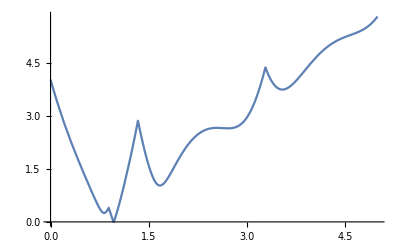

```mathematica
ClearAll["Global`*"]

(* Random Functions *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

MutualTangent[x1_,y1_,r1_,x2_,y2_,r2_]:=Module[{circle1,circle2,h,k,pt,m,l},
(* Returns equation that represents a line when == 0 *)
Return[-2*x*(x1-x2)-2y(y1-y2)-((r1^2-r2^2)-(x1^2-x2^2)-(y1^2-y2^2))];
(* TODO: create exceptions for horizontal and vertical lines *)
];

(* Conversions *)
FtToM=0.3048;
(* Court Dimensions *)
(* TODO: recheck these and make sure the 2in painting is part of calculation *)
ThreePtDistance=22*FtToM;
FoulLineDistance=19*FtToM;
RimToHoop=6/12*FtToM;
RimDiameter=18/12*FtToM;
RimThickness =5/8/12*FtToM;
GroundToRim=10*FtToM;(* ground to top of rim *)
BaselineToBackboard=4*FtToM;
BaselineToRimCenter=63/12*FtToM;
GroundToBackboard=9*FtToM;
BackboardHeight=4*FtToM;
(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;

(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian *)
Iball=2/3*m*rball^2;
KE=1/2*m*(x'[t]^2+y'[t]^2)+1/2*Iball*θ'[t]^2;
PE=m*g*y[t];
L=KE-PE;

(* Euler-Lagrange equations *)
Eq=(Thread[D[L,qᵀ]-D[D[L,dqᵀ],t]==0]);
ELtemp=Solve[Eq[[1]]&&Eq[[2]]&&Eq[[3]],{y''[t],x''[t],θ''[t]}];
EL={y''[t]==ELtemp[[1,1,2]],x''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Hamiltonian *)
p=D[L,dqᵀ];
H=p.dq-L;

(* Impact Equations - solving for velocities after impact *)
(* Impact with ground *)
ϕ0=y[t]-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ0dq1p)/.(y'[t]->ϕ0dq2p)/.(θ'[t]->ϕ0dq3p))-(D[L,dqᵀ])==λ0*D[ϕ0,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ0dq1p)/.(y'[t]->ϕ0dq2p)/.(θ'[t]->ϕ0dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ0dq1p,ϕ0dq2p,ϕ0dq3p,λ0}];
ϕ0dq1p=IEq[[1,1,2]];
ϕ0dq2p=IEq[[1,2,2]];
ϕ0dq3p=IEq[[1,3,2]];
(* Impact with backboard *)
ϕ1=x[t]+rball+BaselineToBackboard;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ1dq1p)/.(y'[t]->ϕ1dq2p)/.(θ'[t]->ϕ1dq3p))-(D[L,dqᵀ])==λ1*D[ϕ1,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ1dq1p)/.(y'[t]->ϕ1dq2p)/.(θ'[t]->ϕ1dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ1dq1p,ϕ1dq2p,ϕ1dq3p,λ1}];
ϕ1dq1p=IEq[[1,1,2]];
ϕ1dq2p=IEq[[1,2,2]];
ϕ1dq3p=IEq[[1,3,2]];
(* Impact with front rim *)
ϕ2=Distance2D[{x[t],y[t]},{-BaselineToBackboard-RimToHoop-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2}]-RimThickness/2-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ2dq1p)/.(y'[t]->ϕ2dq2p)/.(θ'[t]->ϕ2dq3p))-(D[L,dqᵀ])==λ2*D[ϕ2,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ2dq1p)/.(y'[t]->ϕ2dq2p)/.(θ'[t]->ϕ2dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ2dq1p,ϕ2dq2p,ϕ2dq3p,λ2}];
λ1=IEq[[1,4,2]]
λ2=IEq[[2,4,2]]
(* TODO MAKE THIS WORK *)
If[λ1>λ2,λn=1,λn=2]
ϕ2dq1p=IEq[[λn,1,2]];
ϕ2dq2p=IEq[[λn,2,2]];
ϕ2dq3p=IEq[[λn,3,2]];
(*λ=IEq[[1,4,2]]*)
(* Impact with back rim *)
ϕ3=Distance2D[{x[t],y[t]},{-BaselineToBackboard-RimToHoop-RimThickness/2,GroundToRim-RimThickness/2}]-RimThickness/2-rball;
ChangeMomentum=Thread[(D[L,dqᵀ]/.(x'[t]->ϕ3dq1p)/.(y'[t]->ϕ3dq2p)/.(θ'[t]->ϕ3dq3p))-(D[L,dqᵀ])==λ3*D[ϕ3,qᵀ]];
Hn = H;
Hp = H/.(x'[t]->ϕ3dq1p)/.(y'[t]->ϕ3dq2p)/.(θ'[t]->ϕ3dq3p);
ConserveH=(Hp==Hn);
IEq=Solve[ChangeMomentum[[1]]&&ChangeMomentum[[2]]&&ChangeMomentum[[3]]&&ConserveH,{ϕ3dq1p,ϕ3dq2p,ϕ3dq3p,λ3}];
ϕ3dq1p=IEq[[1,1,2]];
ϕ3dq2p=IEq[[1,2,2]];
ϕ3dq3p=IEq[[1,3,2]];


(* Constants *)
g=9.8;

(* Initial Conditions - TODO: replace these with results from shot dynamics.08.08*)
(* Impacts with backboard, front rim *)
(*InitCon={x[0]==-FoulLineDistance,y[0]==6.5*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* Impacts with backboard, back rim *)
(*InitCon={x[0]==-FoulLineDistance,y[0]==5.5*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* Impacts with backboard, MAYBE front rim back rim *)
InitCon={x[0]==-FoulLineDistance,y[0]==5.8*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};
(* Impacts with front rim - short shot *)
(*InitCon={x[0]==-FoulLineDistance,y[0]==4.2*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)
(* over the backboard *)
(*InitCon={x[0]==-FoulLineDistance,y[0]==8.3*FtToM,θ[0]==0,x'[0]==5.0,y'[0]==6.0,θ'[0]==0};*)

(* Numerical Solution *)
(*sol=NDSolve[Join[EL,InitCon],{y,x,θ},{t,0,10}];*)
tmax=5;
newxdot=0;
newydot=0;
newθdot=0;

(* TODO: better options to avoid missing (ex. "back rim" printed when tmax=5, but no change in direction) *)
{sol,{times}}=NDSolve[Join[EL,InitCon,
(* impact with ground *)
{WhenEvent[y[t]-rball==0,{Print["Ground Impact"],end=t,Print[end],newxdot=N[ϕ0dq1p],newydot=N[ϕ0dq2p],newθdot=N[ϕ0dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot},"DetectionMethod"->"Interpolation"]},
(* impact with backboard - TODO: improve y triggers*)
{WhenEvent[x[t]+rball+BaselineToBackboard==0&&y[t]<(GroundToBackboard+BackboardHeight)&&y[t]>GroundToBackboard,{Print["Backboard!"],end=t,Print[end],newxdot=N[ϕ1dq1p],newydot=N[ϕ1dq2p],newθdot=N[ϕ1dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot},"DetectionMethod"->"Interpolation"]},
(* impact with front rim *)
{WhenEvent[Distance2D[{x[t],y[t]},{-BaselineToBackboard-RimToHoop-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2}]-RimThickness/2-rball==0,{Print["Front Rim Impact!"],end=t,Print[end],newxdot=N[ϕ2dq1p],newydot=N[ϕ2dq2p],newθdot=N[ϕ2dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot,Print[newxdot],Print[newydot]},
"DetectionMethod"->"Interpolation",
"IntegrateEvent"->True,
"LocationMethod"->{"Brent",AccuracyGoal->12,PrecisionGoal->12}]},
(* impact with back rim *)
{WhenEvent[Distance2D[{x[t],y[t]},{-BaselineToBackboard-RimToHoop-RimThickness/2,GroundToRim-RimThickness/2}]-RimThickness/2-rball==0,
{Print["Back Rim Impact!"],end=t,Print[end],newxdot=N[ϕ3dq1p],newydot=N[ϕ3dq2p],newθdot=N[ϕ3dq3p],x'[t]->newxdot,y'[t]->newydot,θ'[t]->newθdot,Print[newxdot],Print[newydot]},
"DetectionMethod"->"Interpolation",
"LocationMethod"->{"Brent",AccuracyGoal->12,PrecisionGoal->12}]}
],{x,y,θ},{t,0,tmax}]//Reap;



(*ListPlot[RealExponent[Differences[times]]]*)

xsol=First[x[t]/.sol];
ysol=First[y[t]/.sol];
θsol=First[θ[t]/.sol];

Plot[Distance2D[{xsol,ysol},{-BaselineToBackboard-RimToHoop-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2,0}]-RimThickness/2-rball,{t,0,tmax}]

(* Dynamic Graphics *)
BallGraphic=Circle[{xsol,ysol},diameterBall/2];
BallLineGraphic=Line[{{xsol-rball*Cos[θsol],ysol-rball*Sin[θsol]},{xsol+rball*Cos[θsol],ysol+rball*Sin[θsol]}}];

(* Static Graphics *)
FloorGraphic=Line[{{-22*FtToM,0},{0,0}}];
BackboardGraphic=Line[{{-BaselineToBackboard,GroundToBackboard},{-BaselineToBackboard,GroundToBackboard+BackboardHeight}}];
FrontRimGraphic=Disk[{-BaselineToBackboard-RimToHoop-RimThickness/2-RimDiameter,GroundToRim-RimThickness/2},RimThickness/2];
BackRimGraphic=Disk[{-BaselineToBackboard-RimToHoop-RimThickness/2,GroundToRim-RimThickness/2},RimThickness/2];

Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic
}],
PlotRange->{{-8,1},{-1,6}},
Axes->True,
ImageSize->Full
],
{time,0,tmax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{1000,800}
]

Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic,
Black,BackRimGraphic,
Black,FrontRimGraphic
}],
PlotRange->{{-2.5,-1},{2.5,4.1}},
Axes->True,
ImageSize->Full
],
{time,0,tmax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{800,700}
]
```

## Equations Of Motion (no impact)

```mathematica
(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian *)
Iball=2/3*m*rball^2;
KE=1/2*m*(x'[t]^2+y'[t]^2)+1/2*Iball*θ'[t]^2;
PE=m*g*y[t];
L=KE-PE;

(* Euler-Lagrange equations *)
Eq=(Thread[D[L,qᵀ]-D[D[L,dqᵀ],t]==0]);
ELtemp=Solve[Eq[[1]]&&Eq[[2]]&&Eq[[3]],{y''[t],x''[t],θ''[t]}];
EL={y''[t]==ELtemp[[1,1,2]],x''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Constants *)
g=9.8;

(* Initial Conditions .08.08*)
(* TODO: replace these with results from shot dynamics *)
InitCon={
x[0]==-FoulLineDistance,
y[0]==7*FtToM,
θ[0]==0,
x'[0]==5.0,
y'[0]==6.0,
θ'[0]==0
};

(* Numerical Solution *)
sol=NDSolve[Join[EL,InitCon],{y,x,θ},{t,0,10}];

xsol=First[x[t]/.sol];
ysol=First[y[t]/.sol];
θsol=First[θ[t]/.sol];

(* Dynamic Graphics *)
BallGraphic=Circle[{xsol,ysol},diameterBall/2];
BallLineGraphic=Line[{{xsol-rball*Cos[θsol],ysol-rball*Sin[θsol]},{xsol+rball*Cos[θsol],ysol+rball*Sin[θsol]}}];

(* Static Graphics *)
FloorGraphic=Line[{{-22*FtToM,0},{0,0}}];
BackboardGraphic=Line[{{-BaselineToBackboard,GroundToBackboard},{-BaselineToBackboard,GroundToBackboard+BackboardHeight}}]

Animate[
Show[
Graphics[{
Black,BallGraphic/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,BackboardGraphic
}],
PlotRange->{{-8,1},{-1,6}},
Axes->True
],
{time,0,10},
AnimationRunning->False
]
```

Line[{{-1.2192,2.7432},{-1.2192,3.9624}}]

## Hoop Graphics

```mathematica
x[t]=-FoulLineDistance
y[t]=7*FtToM
θ[t]=Pi/4;

BallGraphic=Circle[{x[t],y[t]},diameterBall/2];
BallLineGraphic=Line[{{x[t]-rball*Cos[θ[t]],y[t]-rball*Sin[θ[t]]},{x[t]+rball*Cos[θ[t]],y[t]+rball*Sin[θ[t]]}}]

Animate[
Show[
Graphics[{
Black,BallGraphic,
Black,BallLineGraphic,
Black,Line[{{-22*FtToM,0},{0,0}}]
}],
PlotRange->{{-8,1},{-1,6}},
Axes->True
],
{t,0,10},
AnimationRunning->False
]
```

-5.7912

2.1336

Line[{{-5.87202,2.05278},{-5.71038,2.21442}}]